# Lab E4: Capacitors and the RC Circuit

## Introduction

This particular lab’s purpose is to understand and get used to the concept of capactiors and the RC circuit. The capactiors are widely used in modern day electronic devices and technology. Any two conducts that are brought near each other form a capacitor. This lab contains two parts to it. The main goal for this lab is to use the fundamental theories of capactiance and get familiarized to various different equipments to measure the capacitance.

## Data

Introduction to Part 1: Capactiance of parallel plates

In this particular part of the lab the purpose is to measure the capacitance of a parallel- plate capicator as a function of the plate seperation. Hence, the permittivity constant Eo using the following equation: C=Eo(A/d).This particular experiment has to be performed on a table made out of wood due to the presence of large, electrically conducting objects, metal tables, affect the delicate capacitance measurement. In order to achiever effective data, we should be a few feet away from the plates and ntoe the capactiance on the meter, this would be considered the zero capacitance. This is because human beings are made up of salty water, an excellent conductor, hence, the presence of human beings can affect the reading if they are too close. The average thickness of the washers should be measured. Then, one by one washers would be added and then take the measurement of the capacitor. In theory, the capacticance must be proportional to 1/d. Signifying that if we were to plot a graph of the Capcitance vs. 1/d the result should be linear. Hence, the value of Eo could be calculated through the measured capacitance, area, and distance. Thus, the comparison between the calculated value and the theoretical value could be done in order to determine the precision and accuracy of our calculated value. We would also compute the average of all the Eo values, the standard deviation and the error of the mean; resulting in acquiring a value of Eo in a standard format.

Part 1 Data:

```mathematica
thirtywash=0.0483;(*30 washers (m)*)
avgwash=thirtywash/30 (*Average of each washer (m)*)
Aplate=0.093; (*Area of the Plates (m^2)*)
Zerocap=-7*10^-15;(*The Zero capacitance (F)*)
Straycap=29*10^-12;(*The Stray Capacitance (F)*)
thickne={0.00161,0.00322,0.00483,0.00644,0.00805,0.00966};(*Thickness of each washer from 1 to 6 (m)*)
Capacitance={5.08*10^-10,2.74*10^-10,1.93*10^-10,1.53*10^-10,1.32*10^-10,1.18*10^-10}; (*Capacitance of each washer respectively (F)*)
Washers= {1,2,3,4,5,6}; (*Amount of washers*)
Interplatecapcitance= Capacitance-Straycap; (*Interplate Capacitance (F)*)
ood=1/thickne; (*1/d in (m)*)
Ptable=Thread[{Washers,thickne,Capacitance,Interplatecapcitance, ood}];
Grid[ Prepend[Ptable, {"Washers", "Thickness (m)", "Capacitance (F)", "Interplate Capacitance (F)", "1/d (m)"}], Frame -> All]
```

0.00161

Washers | Thickness (m) | Capacitance (F) | Interplate Capacitance (F) | 1/d (m)
1 | 0.00161 | 5.08×10^-10 | 4.79×10^-10 | 621.118
2 | 0.00322 | 2.74×10^-10 | 2.45×10^-10 | 310.559
3 | 0.00483 | 1.93×10^-10 | 1.64×10^-10 | 207.039
4 | 0.00644 | 1.53×10^-10 | 1.24×10^-10 | 155.28
5 | 0.00805 | 1.32×10^-10 | 1.03×10^-10 | 124.224
6 | 0.00966 | 1.18×10^-10 | 8.9×10^-11 | 103.52

Introduction to Part 2:

In this particular part of the lab, the exponential decay of the voltage on a capacitor in an RC circuit using the digital oscilloscope will be observed.The time constant T of the decay would be measured and then we will compare with the computed T=RC. In this part change the time and observe the change in voltage, it helps in determining the time constant T. We will start by recording the voltage and time of 10 or more points along the exponential decay, including 5/6 points int he first part fo the curve between the initial voltage Vo and Vo/3. Theoretically, after ploting out data of V vs. T and ln(V) vs. T, T should be a straight line with a slope of -1/T.

Part 2 Data:

```mathematica
Cap2=2.26*10^-5; (*Capactiance (F)*)
Resis= 993; (*Resistance (Ohm)*)
RC=0.022; (*RC (F(ohm))*)
T= {0.000,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.010,0.013,0.017}; (*Time in (s)*)
Volt={3.62,3.50,3.26,2.74,2.46,2.26,2.10,1.94,1.82,1.66,1.42,1.14}; (*Voltage readings (V)*)
Ntable=Thread[{T,Volt}];
NumberForm[Grid[ Prepend[Ntable, {"Time (s)", "Voltage (V)"}], Frame -> All], {10,3}]
lnv= Log[Volt] (*The natural log of Voltage (V)*)
naturallog=lnv
```

Time (s) | Voltage (V)
0.000 | 3.620
0.002 | 3.500
0.003 | 3.260
0.004 | 2.740
0.005 | 2.460
0.006 | 2.260
0.007 | 2.100
0.008 | 1.940
0.009 | 1.820
0.010 | 1.660
0.013 | 1.420
0.017 | 1.140

{1.28647,1.25276,1.18173,1.00796,0.900161,0.815365,0.741937,0.662688,0.598837,0.506818,0.350657,0.131028}

{1.28647,1.25276,1.18173,1.00796,0.900161,0.815365,0.741937,0.662688,0.598837,0.506818,0.350657,0.131028}

## Data Analyisis:

Part 1:

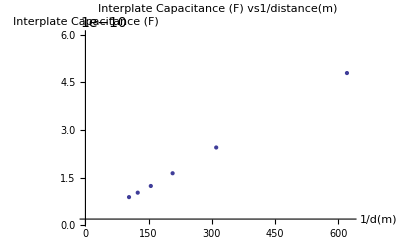

```mathematica
Cvsd = Thread[{ood, Interplatecapcitance}]; 
ListPlot[{Cvsd}, PlotLabel -> "Interplate Capacitance (F) vs1/distance(m)", AxesLabel -> {"1/d(m)","Interplate Capacitance (F)"}, PlotRange -> {{0.00,630}, {0.1*10^-10,6.0*10^-10}}]
```

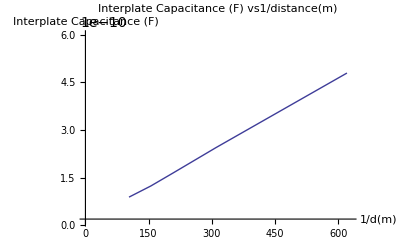

```mathematica
ListLinePlot[{Cvsd},PlotLabel->"Interplate Capacitance (F) vs\!\(\*FractionBox[\(1\), \(distance\)]\)(m)",AxesLabel->{"\!\(\*FractionBox[\(1\), \(d\)]\)(m)","Interplate Capacitance (F)"},PlotRange->{{0.,630},{0.1/10^10,6./10^10}}]
```

We stated that theoretically the plot should have a straight line because the Capacitance is proportional to 1/distance. This is trube because C=Eo(A/d), according to the equation our slope should m=EoA. The slope turned out to be a straight line, thus the results are in direct corrolation with the theorey.

```mathematica
Enot= (Interplatecapcitance*thickne)/Aplate; (*Enot values for each of the washers (F/m)*)
Qtable=Thread[{Washers, Enot}];
NumberForm[Grid[ Prepend[Qtable, {"Washer", "Value of Eo (F/m)"}], Frame -> All], {10,2}]
Avgenot=Mean[Enot](*Average Eo value (F/m)*)
stdv= StandardDeviation[Enot] (*Standard Deviation (F/m)*)
numb=6; (*Number of Washers used*)
stdvmean= stdv/(√numb)(*Standard deviation of the mean (F/m)*)
theoenot=8.854187817*10^-12; (*The theoretical Eo value (F/m)*)
discrep= theoenot-Avgenot(*Discrepency between our calculated value and theoretical value in (F/m)*)
```

Washer | Value of Eo (F/m)
1.00 | 8.29×10^-12
2.00 | 8.48×10^-12
3.00 | 8.52×10^-12
4.00 | 8.59×10^-12
5.00 | 8.92×10^-12
6.00 | 9.24×10^-12

8.67323×10^-12

3.4589×10^-13

1.41209×10^-13

1.80962×10^-13

Since we had the capacitance, the Area, and the distance, we could easily find the Eo value for each of the different washers (presented above in the table). Thus the Average Eo value could be calculated: 8.67*10^-12(F/m).The standard deviation being 3.46*10^-13(F/m) and the standard deviation of the mean being 1.41*10^-13(F/m). Thus the actual standard deviation calculated is (8.67±0.14) *10^-12(F/m). The discrepency between the calculated and theoretical is 1.81*10^-13(F/m).

Part 2:

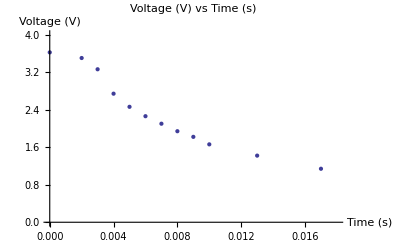

```mathematica
Tvsvolt = Thread[{T, Volt}]; 
ListPlot[{Tvsvolt}, PlotLabel -> "Voltage (V) vs Time (s)", AxesLabel -> {"Time (s)","Voltage (V)"}, PlotRange -> {{0.00,0.018}, {0.0,4}}]
```

This plot as expected wouldn’t tell us anything. It was suppose to be a curved plot.

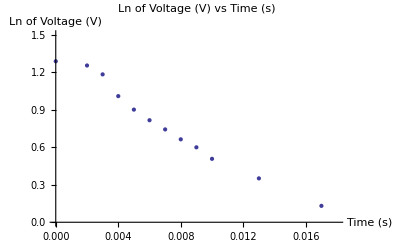

```mathematica
lnVvsT = Thread[{T, lnv}]; 
ListPlot[{lnVvsT}, PlotLabel -> "Ln of Voltage (V) vs Time (s)", AxesLabel -> {"Time (s)","Ln of Voltage (V)"}, PlotRange -> {{0.00,0.018}, {0.0,1.5}}]
```

This plot of Ln(V) vs. Time, in theory, should be a straight line with a slope of -1/T constant. Its not completely stragight (but it is getting there). This limitation could have been a result of internal resistance and capacitance of the wires. And the capacitors are very sensitive, any material nearby could have impacted on the final result/reading. Now using the linfit.nb file, one can determine the best fit line, slope, uncertainity in the slope, intercept, and uncertainty in the intercept. Hence, the time constant can be calculated.

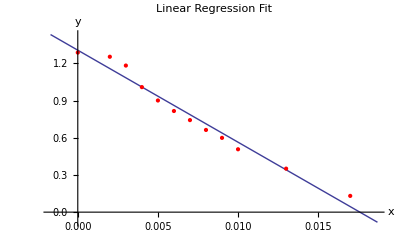

```mathematica
mic=-74.176;
δmic=3.930;
b=1.306;
δb=0.033;
Tim=-1/mic(*The T value in (s)*)
δTim=(1/mic^2)δm(*Uncertainity using the rule of error propagation (s)*)
Discrep2=RC-Tim (*Discrepency between the RC value and the calculated T (s)*)
```

0.0134814

0.000714275

0.00851855

T=0.014 ± 0.001 s with a Discrepency of 0.009 s.

## Conclusion

Part 1: Capacitance of Parallel Plates

The Average Eo value was calculated to be: 8.67*10^-12(F/m).The standard deviation being 3.46*10^-13(F/m) and the standard deviation of the mean being 1.41*10^-13(F/m). Thus the actual standard deviation calculated is (8.67±0.14) *10^-12(F/m). The discrepency between the calculated and theoretical is 1.81*10^-13(F/m). The discrepency between the theoretical and experimental is rather small, signifying that the lab was actually succesful in terms of precision. Although the possible limitations (sources of erros) could have been caused by the fact that there were many different objects nearby the capacitance. Since the capcitors are extremely sensitive, the human bodies can also be taken into account for the limitations of the accuracy and precision of the results. Even the environment in which the lab was conducted could be a factor into the lab errors/limitations (like exisiting heat in the environment will degrade its performance as well). The material tha the capacitor was made out of also affects the results.  The lab could improve if we chose a different setting for the lab to be conducted, like in some sort of vaccum, the results could be better and more accurate.In theory the plot between the interplate capacitance against the inverse distance was supposed to be a straight line with a slope of m=EoA, which experimentally, was exactly what occured.

Part 2: Measurement of the time constant of an RC circuit

In the second part of this particular lab, the exponential decay of the voltage on a capacitor in an RC circuit using a digital oscilloscope was observed. Using all our data, we plotted a graph of the change in voltage vs.time. It doesn’t help us conclude anything, thus the plot of Ln(V) vs. Time was created, which in theory should’ve given a perfect straight line. However, that could occur in a perfect world, thus our’s was close enough to a straight line. Hence, the linfit.nb file was used in order to create a best fit line for the plotted points as seen above in the data analysis. Then the data that the linfit.nb provided (the best fit line, slope, uncertainity in the slope, intercept, and uncertainty in the intercept), we used to determine the Time constant to be 0.014s. The RC value was 0.022s, which gave a discrepency of 0.009s. Not a very high discrepency, but it is significant enough. The possible limitations could be the resistance and the capacitance of the wires. The values of internal resistance were not taken into account, nor did we know about the commerical resistor and the capacitor (which could be a major factor in error). The oscilloscope was not really functioning properly at the beginning, might’ve been a factor in the limitation. In conclusion, this lab taught us about capacitors and time constants.